```mathematica
DSolve[{D[u[x,t], t]+a*D[u[x,t],x]==0}, u[x,t], {x,t}][[1,1]]
```

u[x,t]→C[1][t-x/a]

```mathematica
DSolve[{D[u2[x,t], t]+a[x]*D[u2[x,t],x]==0}, u2[x,t], {x,t}][[1,1]]
```

u2[x,t]→C[1][t-1/a[K[1]]K[1]1x]

```mathematica
DSolve[{D[u3[x,t], t]+a[x,t]*D[u3[x,t],x]==0}, u3[x,t], {x,t}][[1,1]]
```

u3^(0,1)[x,t]+a[x,t] u3^(1,0)[x,t]==0

Подстановка в PDE (должно быть 0): 0

-Graphics3D-

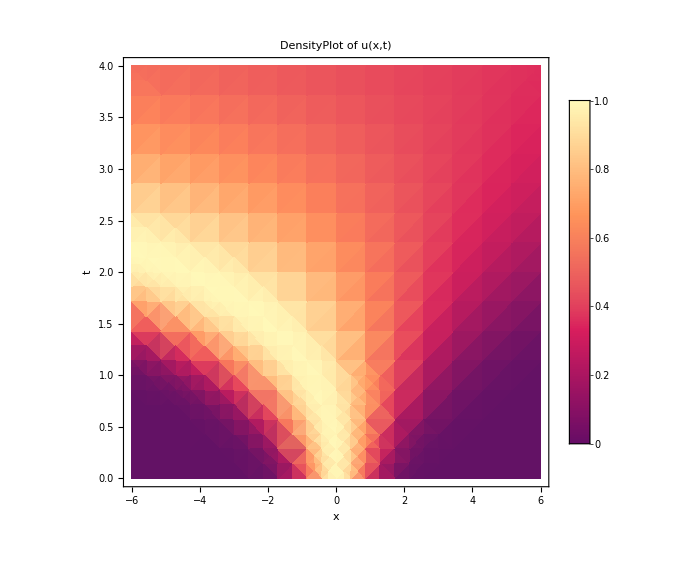

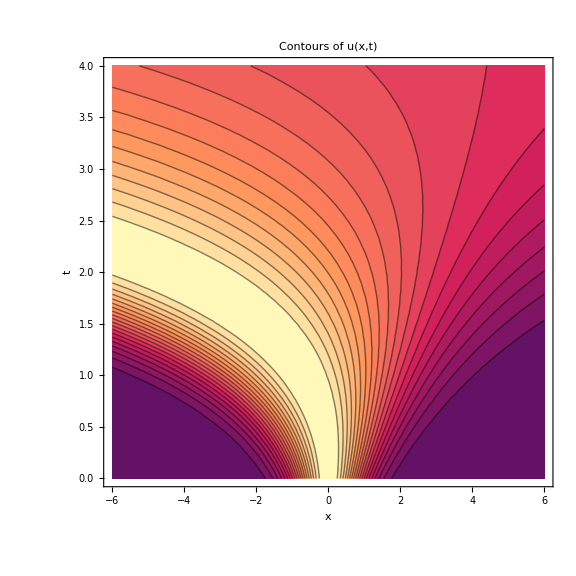

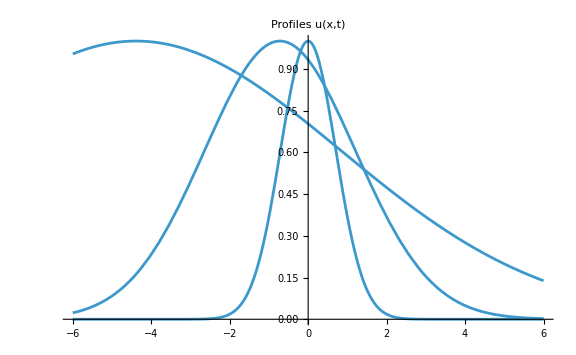

Table::itform: Argument {xi,-3,-1,0,1,2,3,5} at position 2 does not have the correct form for an iterator.

General::stop: Further output of Table::itform will be suppressed during this calculation.

-Graphics-

ParametricPlot::pllim: Range specification {xi,-3,3,1} is not of the form {x, xmin, xmax}.

Show::gcomb: Could not combine the graphics objects in Show[,ParametricPlot[{X[s,xi],s},{s,0,4},{xi,-3,3,1},PlotStyle→Thin],PlotRange→{{-6,6},{0,4}},AxesLabel→{x,t},ImageSize→Large].

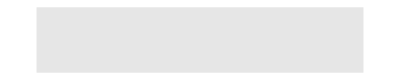
Show[-Graphics-,ParametricPlot[{X[s,xi],s},{s,0,4},{xi,-3,3,1},PlotStyle→Thin],PlotRange→{{-6,6},{0,4}},AxesLabel→{x,t},ImageSize→Large]

```mathematica
(*----------------------------------------------------------------------*)(*1) Определим начальную функцию u0.Меняйте на любую другую по желанию*)(*----------------------------------------------------------------------*)u0[x_]:=Exp[-x^2]        (*пример:гаусс*)

(*----------------------------------------------------------------------*)
(*2) Аналитическое решение,вывезенное методом характеристик*)
(*(для a(x,t)=x-t и начального условия u(x,0)=u0(x))*)
(*----------------------------------------------------------------------*)
uSol[x_,t_]:=u0[1+(x-t-1) Exp[-t]]

(*----------------------------------------------------------------------*)
(*3) Быстрая проверка:подстановка в PDE u_t+(x-t) u_x==0*)
(*(SymbolicSimplify должен вернуть True)*)
(*----------------------------------------------------------------------*)
pdeCheck=FullSimplify[D[uSol[x,t],t]+(x-t) D[uSol[x,t],x]];
Print["Подстановка в PDE (должно быть 0): "<>ToString[pdeCheck]];

(*----------------------------------------------------------------------*)
(*4) Plot3D—поверхность u(x,t)*)
(*----------------------------------------------------------------------*)
Plot3D[uSol[x,t],{x,-6,6},{t,0,4},AxesLabel->{"x","t","u(x,t)"},PlotRange->All,Mesh->None,PlotLabel->"u(x,t) = u0(1+(x-t-1) e^{-t})",ImageSize->Large]

(*----------------------------------------------------------------------*)
(*5) DensityPlot (тепловая карта) и контурная карта*)
(*----------------------------------------------------------------------*)
DensityPlot[uSol[x,t],{x,-6,6},{t,0,4},FrameLabel->{"x","t"},PlotLabel->"DensityPlot of u(x,t)",PlotLegends->Automatic,ImageSize->Large]

ContourPlot[uSol[x,t],{x,-6,6},{t,0,4},Contours->20,FrameLabel->{"x","t"},PlotLabel->"Contours of u(x,t)",ImageSize->Large]

(*----------------------------------------------------------------------*)
(*6) Профиль по x при фиксированном t:статический и анимированный*)
(*----------------------------------------------------------------------*)
(*статический профиль при t=0,1,2*)
Show[Plot[uSol[x,0],{x,-6,6},PlotRange->All,PlotLabel->"Profiles u(x,t)"],Plot[uSol[x,1],{x,-6,6}],Plot[uSol[x,2],{x,-6,6}],PlotLegends->{"t=0","t=1","t=2"},ImageSize->Large]

(*анимация с слайдером*)
Manipulate[Plot[uSol[x,t0],{x,-6,6},PlotRange->All,AxesLabel->{"x","u"}],{{t0,0,"t"},0,4}]

(*----------------------------------------------------------------------*)
(*7) Визуализация характеристик:решения ODE dx/dt=x-t*)
(*X(t;xi)=t+1+(xi-1) e^t*)
(*----------------------------------------------------------------------*)
X[t_,xi_]:=t+1+(xi-1) Exp[t]

(*несколько характеристик для разных xi*)
ParametricPlot[Evaluate[Table[{X[s,xi],s},{xi,-3,-1,0,1,2,3,5}]],{s,0,4},AxesLabel->{"x","t"},PlotLegends->Placed[LineLegend[ToString/@({-3,-1,0,1,2,3,5})],Right],PlotLabel->"Characteristics x(t; xi) for various xi",ImageSize->Large]

(*Наложить уровни u0 на t=0 и соответствующие значения u на других t*)
Show[Graphics[{GrayLevel[0.9],Rectangle[{-6,-0.2},{6,0}]}],ParametricPlot[{X[s,xi],s},{s,0,4},{xi,-3,3,1},PlotStyle->Thin],PlotRange->{{-6,6},{0,4}},AxesLabel->{"x","t"},ImageSize->Large]

(*----------------------------------------------------------------------*)
(*8) Пример:поменять u0 на другую и посмотреть снова*)
(*----------------------------------------------------------------------*)
(*Пример:шаг в коде:u0[x_]:=Sin[x] или u0[x_]:=1/(1+x^2) и т.д.*)
```

```mathematica
DSolve[{D[u[x,t], t]+a*D[u[x,t],x]==0,u[x,0]==u0[x]}, u[x,t], {x,t}][[1,1]]
```

u[x,t]→u0[-a (t-x/a)]

```mathematica
DSolve[{D[u1[x,t], t]+a[x]*D[u1[x,t],x]==0}, u1[x,t], {x,t}][[1,1]]
```

u1[x,t]→C[1][t-1/a[K[1]]K[1]1x]

```mathematica
Clear[sol];
sol=u1[x,t]/.DSolve[{D[u1[x,t], t]+a[x]*D[u1[x,t],x]==0}, u1[x,t], {x,t}][[1,1]]
```

C[1][t-1/a[K[1]]K[1]1x]

```mathematica
Activate[sol/.a[x_]->Exp[k*x]]
```

C[1][-(ⅇ^-k-ⅇ^(-k x))/k+t]

```mathematica
DSolve[{D[u2[x,t], t]+a[t]*D[u2[x,t],x]==0}, u2[x,t], {x,t}][[1,1]]
```

u2[x,t]→C[1][-x+a[K[1]]K[1]1t]

```mathematica
sol1 = u2[x,t]/.DSolve[{D[u2[x,t], t]+a[t]*D[u2[x,t],x]==0}, u2[x,t], {x,t}][[1,1]]
```

C[1][-x+a[K[1]]K[1]1t]

```mathematica
Activate[sol1/.a[t_]->1]
```

C[1][-1+t-x]

```mathematica
DSolve[{D[u3[x,t], t]+(x-t)*D[u3[x,t],x]==0}, u3[x,t], {x,t}][[1,1]]
```

DSolve::ifun: Inverse functions are being used by DSolve, so some solutions may not be found.

u3[x,t]→C[1][ⅇ^-t (-1-t+x)]

```mathematica
DSolveValue[D[u[x,t],t]+(x-t) D[u[x,t],x]==0,u[x,t],{x,t}]
```

DSolveValue::ifun: Inverse functions are being used by DSolveValue, so some solutions may not be found.

C[1][ⅇ^-t (-1-t+x)]

```mathematica
DSolve[{D[u4[x,t], t]+a[x-t]*D[u4[x,t],x]==0}, u4[x,t], {x,t}][[1,1]]
```

DSolve::nlpde: Solution requested to nonlinear partial differential equation. Trying to build a special solution.

u4[x,t]→C[2]+-C[1]/(-1+a[-t+K[1]])K[1]1x+(a[x-K[6890]] C[1]+-(C[1] a'[K[1]-K[6890]])/(-1+a[K[1]-K[6890]])^2K[1]1x-a[x-K[6890]] -(C[1] a'[K[1]-K[6890]])/(-1+a[K[1]-K[6890]])^2K[1]1x)/(-1+a[x-K[6890]])K[6890]1t

```mathematica
Clear[u,a]

s[x_,t_]:=x-t;

chi[x_,t_]:=Integrate[1/(a[s]-1),s]-t;

u[x_,t_]:=F[chi[x,t]]
```

```mathematica
u[x,t]
```

F[-t+∫1/(-1+a[s])ⅆs]

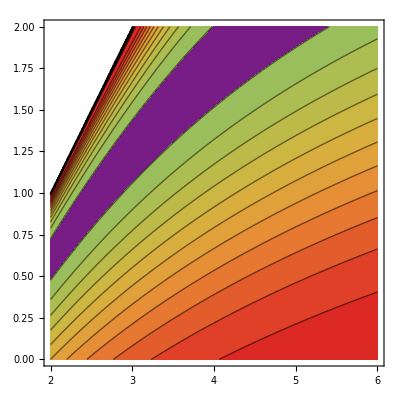

```mathematica
Clear[u,a,chi,F]

a[s_]:=s;

chi[x_,t_]:=Log[x-t-1]-t;

F[z_]:=Sin[z];    (*любое начальное условие*)

u[x_,t_]:=F[chi[x,t]];

ContourPlot[u[x,t],{x,2,6},(*область где x-t-1>0*){t,0,2},Contours->20,ColorFunction->"Rainbow",PlotPoints->40]
```

```mathematica
Clear[a,s,chi,u,F]

a[s_]:=s;
s[x_,t_]:=x-t;

chi[x_,t_]:=Log[Abs[s[x,t]-1]]-t;

F[z_]:=Sin[z];

u[x_,t_]:=F[chi[x,t]];

Plot3D[u[x,t],{x,-10,4},{t,-2,10},PlotRange->All,Mesh->None,ColorFunction->"Rainbow",AxesLabel->{"x","t","u"},PlotPoints->80]
```

-Graphics3D-

```mathematica
a=1; (*скорость переноса*)

(*---Определяем функции---*)
uStep[x_,t_]:=HeavisideTheta[x-a*t]                        (*1. Ступенька*)
uSmooth[x_,t_]:=Tanh[x-a*t]                                (*2. Гладкая возрастающая*)
uSignChange[x_,t_]:=Sin[x-a*t]                              (*3. Меняет знак*)
uTwoFronts[x_,t_]:=HeavisideTheta[x+2-a*t]+HeavisideTheta[x-3-a*t]  (*4. Два фронта*)

(*---Manipulate для динамики---*)
Manipulate[Plot[{uStep[x,t],uSmooth[x,t],uSignChange[x,t],uTwoFronts[x,t]},{x,-10,10},PlotRange->{-1,3},PlotStyle->{Orange,Blue,Green,Purple},PlotLegends->{"Step","Smooth","Sign Change","Two Fronts"},AxesLabel->{"x","u(x,t)"}],{t,0,10}]
```

```mathematica
a=1; (*скорость переноса*)

(*---Определяем функции---*)
uStep[x_,t_]:=HeavisideTheta[x-a*t]
uSmooth[x_,t_]:=Tanh[x-a*t]
uSignChange[x_,t_]:=Sin[x-a*t]
uTwoFronts[x_,t_]:=HeavisideTheta[x+2-a*t]+HeavisideTheta[x-3-a*t]

(*---3D графики---*)
Plot3D[uStep[x,t],{x,-10,10},{t,0,10},PlotRange->{0,2},AxesLabel->{"x","t","u"},PlotLabel->"Step Function",Mesh->None,ColorFunction->"OrangeRed"]

Plot3D[uSmooth[x,t],{x,-10,10},{t,0,10},PlotRange->{-1,1},AxesLabel->{"x","t","u"},PlotLabel->"Smooth Increasing",Mesh->None,ColorFunction->"BlueGreen"]

Plot3D[uSignChange[x,t],{x,-10,10},{t,0,10},PlotRange->{-1,1},AxesLabel->{"x","t","u"},PlotLabel->"Sign Change",Mesh->None,ColorFunction->"Rainbow"]

Plot3D[uTwoFronts[x,t],{x,-10,10},{t,0,10},PlotRange->{0,2},AxesLabel->{"x","t","u"},PlotLabel->"Two Fronts",Mesh->None,ColorFunction->"PurpleTones"]
```

Plot3D::cfun: The value of the option ColorFunction -> OrangeRed is not a valid color function or a gradient ColorData entity.

-Graphics3D-

Plot3D::cfun: The value of the option ColorFunction -> BlueGreen is not a valid color function or a gradient ColorData entity.

-Graphics3D-

-Graphics3D-

Plot3D::cfun: The value of the option ColorFunction -> PurpleTones is not a valid color function or a gradient ColorData entity.

-Graphics3D-

```mathematica
a[x_]:=1+0.5*Sin[x]

(*---Численный аргумент характеристики---*)
charArg[x_?NumericQ,t_]:=Module[{xmin,xmax},If[x>=0,xmin=0;xmax=x,xmin=x;xmax=0];
t-NIntegrate[1/a[s],{s,xmin,xmax}]]

(*---Начальные условия---*)
fStep[s_]:=HeavisideTheta[s]
fSmooth[s_]:=Tanh[s]
fSignChange[s_]:=Sin[s]
fTwoFronts[s_]:=HeavisideTheta[s+2]+HeavisideTheta[s-3]

(*---Решения---*)
uStep[x_,t_]:=fStep[charArg[x,t]]
uSmooth[x_,t_]:=fSmooth[charArg[x,t]]
uSignChange[x_,t_]:=fSignChange[charArg[x,t]]
uTwoFronts[x_,t_]:=fTwoFronts[charArg[x,t]]

(*---Manipulate для динамики---*)
Manipulate[Plot[Evaluate[{uStep[x,t],uSmooth[x,t],uSignChange[x,t],uTwoFronts[x,t]}],{x,-10,10},PlotRange->{-1,3},PlotStyle->{Orange,Blue,Green,Purple},PlotLegends->{"Step","Smooth","Sign Change","Two Fronts"},AxesLabel->{"x","u(x,t)"}],{t,0,10}]
```

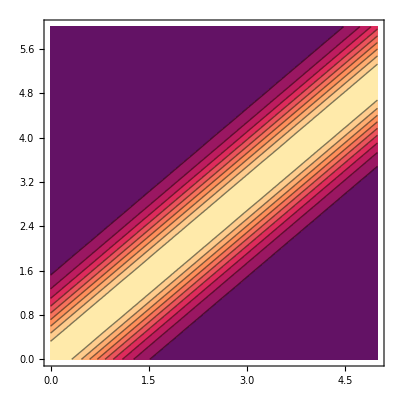

```mathematica
a=1;
phi1[z_]:=Exp[-z^2]
phi[x_,t_]:=phi1[x-a*t];
ContourPlot[phi[x, t], {x,0,5}, {t,0,6}]
```

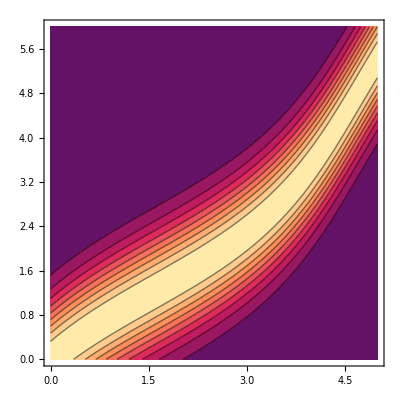

-Graphics3D-

```mathematica
ClearAll["Global`*"]
a[x_]:=1+0.5*Sin[x];
fsol=NDSolve[{f'[x]==1/a[x],f[0]==0},f,{x,0,5}][[1]];
phi0[z_]:=Exp[-z^2];
u[x_?NumericQ,t_?NumericQ]:=phi0[t-(f[x]/. fsol)];
ContourPlot[u[x,t],{x,0,5},{t,0,6},PlotPoints->50]
Plot3D[u[x,t],{x,0,5},{t,0,6}]
```

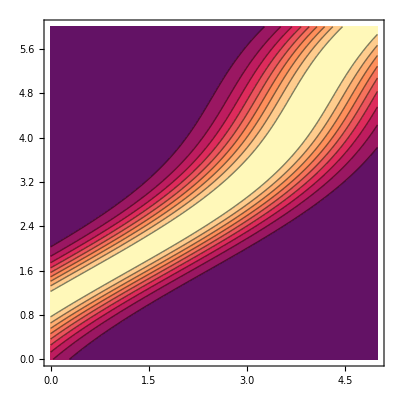

-Graphics3D-

```mathematica
ClearAll["Global`*"]
a[t_]:=1+0.5*Sin[t];

fsol=NDSolve[{f'[t]==a[t],f[1]==0},f,{t,0,6}][[1]];
phi0[z_]:=Exp[-z^2];
u[x_?NumericQ,t_?NumericQ]:=phi0[-x+(f[t]/. fsol)];
ContourPlot[u[x,t],{x,0,5},{t,0,6},PlotPoints->50]
Plot3D[u[x,t],{x,0,5},{t,0,6}]
```

General::munfl: Exp[-7.7571×10^9] is too small to represent as a normalized machine number; precision may be lost.

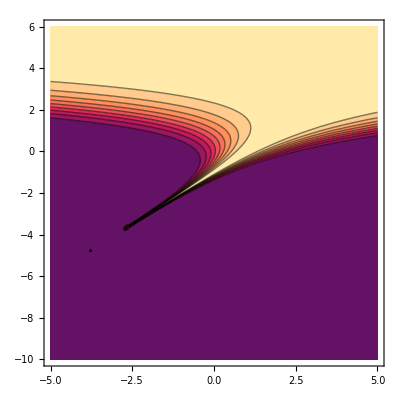

General::munfl: Exp[-7.74324×10^9] is too small to represent as a normalized machine number; precision may be lost.

-Graphics3D-

```mathematica
ClearAll["Global`*"]
phi0[z_]:=Exp[-z^2];
u[x_?NumericQ,t_?NumericQ]:=phi0[Exp[-t]*(x-1-t)];
ContourPlot[u[x,t],{x,-5,5},{t,-10,6},PlotPoints->50]
Plot3D[u[x,t],{x,-5,5},{t,-10,6}, PlotRange->All]
```

```mathematica
ClearAll["Global`*"]
phi0[z_]:=Exp[-z^2];
a1[z_]:=1+0.5*Sin[z];
u[x_?NumericQ,t_?NumericQ]:=Module[{xi0,sol},
sol=NDSolveValue[{f'[τ]==a1[f[τ]]-1,f[t]==x-t},f,{τ,0,t}];
xi0=sol[0];
phi0[xi0]];
ContourPlot[u[x,t],{x,-5,15},{t,0,8},PlotPoints->50]
Plot3D[u[x,t],{x,-5,15},{t,0,8},PlotRange->All]
```

-Graphics-

-Graphics3D-